```mathematica
Quit[];
```

# Problem 3: ergodic metric

## System description

The system could be a spring-mass-damper. This will provide intuition about how damping affects ergodicity. In the phase plane, the trajectory is circular when there is no damping.

State space model

```mathematica
A={{0,1},{-1,b}};
ssm=x'[t]==A.x[t];
n=First[Dimensions[A]];
```

Initial conditions, timestep size, and terminal time

```mathematica
ICs=x[0]=={{0},{1}};
dt=0.1;(*the system has natural frequency 1, choose dt appropriately*)
T=10;
```

Numerical simulation

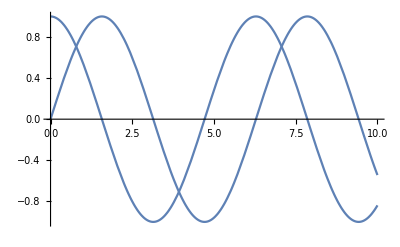

InterpolatingFunction[{{0., 10.}}, <>][t]

```mathematica
sol=NDSolve[{ssm/.b->-0.0,ICs},{x},{t,0,T}];
Plot[Evaluate[x[t]/.sol],{t,0,T}]
xt=x[t]/.First[sol](*RESUME HERE*)
```

Distribution w.r.t. which we care about ergodicity

```mathematica
μ=0;
Σ=DiagonalMatrix[{2,2}];
ϕ[x_]:=Det[2 Pi Σ]^-1 Exp[-1/2(x-μ)ᵀ.Inverse[Σ].(x-μ)];
```

## Ergodic metric

Functions that are evaluated at every timestep

```mathematica
K=4;(*length of Fourier expansion, consider accuracy vs computation time*)
L1=4;(*length of dimension 1 of state????*)
L2=4;(*length of dimension 2 of state????*)
L={{L1},{L2}};
Λ[k_]:=(1-Norm[k,2]^2)^(-((n+1)/2));
h[k_]:=(∫_0^L1 ∫_0^L2 Cos[((k[[1,1]] Pi)/L1) x1]^2 Cos[((k[[2,1]] Pi)/L1) x1]^2 ⅆx2ⅆx1)^(1/2);
F[k_,xt_]:=1/h[k]∏_(i=1)^n Cos[(k[[i,1]] Pi)/L[[i,1]] xt[[i,1]]]
```

√(4+Sin[2 (k1-k2) π]/(k1 π-k2 π)+((2 Sin[2 k1 π])/k1+(2 Sin[2 k2 π])/k2+Sin[2 (k1+k2) π]/(k1+k2))/π)

√(4+Sin[2 (k1-k2) π]/(k1 π-k2 π)+((2 Sin[2 k1 π])/k1+(2 Sin[2 k2 π])/k2+Sin[2 (k1+k2) π]/(k1+k2))/π)

```mathematica
ϕt={First[ϕ[First[x[0]/.sol]]]};
For[t=0,t<T,t=t+dt;AppendTo[ϕt,First[ϕ[First[x[t]/.sol]]]]];
```